Select the parameter (.prm) file of the desired chromatogram. It is assumed that the chromatography files are in the same directory as the parameter file.

```mathematica
SystemDialogInput["FileOpen" , {"C:/Users/fskdm/Dropbox", {"Parameter Files"->{"*.prm"}}}]
```

```mathematica
pfile ="C:\\Users\\fskdm\\My PhD\\Projects\\2019_12_20_PhD_Last_Project\\2019_12_23_PAH_FAMEs\\Chromatograms\\RawData\\2020_02_11-120014.dat.prm"
```

C:\Users\fskdm\My PhD\Projects\2019_12_20_PhD_Last_Project\2019_12_23_PAH_FAMEs\Chromatograms\RawData\2020_02_11-120014.dat.prm

```mathematica
(*Extract the data directory:*)
filedir = FileNameJoin[ FileNameSplit[pfile][[1;;-2]]];

(*Import the parameters:*)
params = Import[pfile, "Lines"];

(*Create the data filename*)
file= FileNameJoin[
		{filedir
	,	FileNameSplit[
		StringSplit[                         
			params[[15]]                    (* Line 15 of the paramaters file contains the name of the data file *)
		][[3]]]                                        (* It is the third part of the line as separated by whitespace *)
		[[-1]]                                                 (* Select the last item on the list of the stringsplit *)
		}
	];(* Extract the filename *)
(* Show the result *)
Framed[TabView[{"Data"-> TableForm[{filedir, file}], "Parameters" -> params}]]
```

12

```mathematica
FrontEndTokenExecute["SaveRename", {StringJoin[file,".nb"]}]
```

```mathematica
data=BinaryReadList[file, {"Integer8"}~Join~Table["Real64", {17}], ByteOrdering->-$ByteOrdering];
```

```mathematica
Length[data[[1]]]
```

18

```mathematica
data[[-5;;-1]]//TableForm
```

2 | 12.053 | 304.971 | 295.585 | 5.08353 | 5.37492 | 2.03269×10^7 | 45207.9 | 650.815 | 649.011 | 0.0079895 | 628.947 | -0.0573669 | 2.0265×10^7 | 2.76769×10^7 | 678.15 | 673.15 | 623.15
2 | 12.075 | 304.97 | 295.569 | 5.08379 | 5.3752 | 2.03257×10^7 | 46877.7 | 650.727 | 648.883 | 0.00800171 | 628.948 | -0.0570801 | 2.0265×10^7 | 2.76769×10^7 | 678.15 | 673.15 | 623.15
2 | 12.098 | 304.97 | 295.57 | 5.08413 | 5.37493 | 2.03264×10^7 | 46259.2 | 650.772 | 648.942 | 0.0078949 | 628.823 | -0.0572754 | 2.0265×10^7 | 2.76769×10^7 | 678.15 | 673.15 | 623.15
3 | 1080. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4 | 1080. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

```mathematica
data[[1;;5]]//TableForm
```

0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1 | 659.9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2 | 0.033 | 302.383 | 294.455 | 2.71312 | 1.58794 | 2.01904×10^7 | 141159. | 598.624 | 600.922 | 0.0151398 | 226.334 | -0.0483612 | 2.0265×10^7 | 2.76769×10^7 | 623.15 | 623.15 | 253.15
2 | 0.056 | 302.384 | 294.452 | 2.55081 | 1.50877 | 2.0191×10^7 | 138870. | 598.699 | 600.968 | 0.0170349 | 226.334 | -0.0465698 | 2.0265×10^7 | 2.76769×10^7 | 623.15 | 623.15 | 253.15
2 | 0.08 | 302.383 | 294.453 | 2.53409 | 1.50473 | 2.01887×10^7 | 141035. | 598.66 | 600.911 | 0.0163208 | 226.334 | -0.0470184 | 2.0265×10^7 | 2.76769×10^7 | 623.15 | 623.15 | 253.15

Plot the manifold temperatures:

```mathematica
ListPlot[{data[[All,9]]-273.12, data[[All, 10]]- 273.12,data[[All, 16]]- 273.12,data[[All,17]]- 273.12}
, PlotRange->{320, 400}
(*, PlotLegends->{"Inlet","Detector","Setpoint I","Setpoint D"} *)
, PlotLegends->SwatchLegend[{"Inlet","Detector","Setpoint I","Setpoint D"} ,LegendLabel->"Legend",LegendFunction->(Framed[#,Background->LightBlue]&)]
, AxesLabel->{"Sample","Manfold Temperature (°C)"}
, ImageSize->Large
,PlotLabel->"Reported Manifold temperatures"

]
```

-Graphics-

Just plot the temperatures:

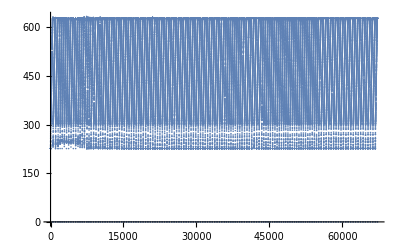

```mathematica
ListPlot[data[[All,12]]]
```

```mathematica
values={"ID", "Time", "TAmbient", "Ttc", "Vb", "dV", "P1", "P2", "TInlet", "TOutlet", "Detector", "TColumn", "Vcol","P1 Setpoint", "P2 Setpoint", "TInlet Setpoint", "TOutlet Setpoint", "TColumn Setpoint"}
```

{ID,Time,TAmbient,Ttc,Vb,dV,P1,P2,TInlet,TOutlet,Detector,TColumn,Vcol,P1 Setpoint,P2 Setpoint,TInlet Setpoint,TOutlet Setpoint,TColumn Setpoint}

```mathematica
Join[{values}, {Range[18] } ]//TableForm
```

ID | Time | TAmbient | Ttc | Vb | dV | P1 | P2 | TInlet | TOutlet | Detector | TColumn | Vcol | P1 Setpoint | P2 Setpoint | TInlet Setpoint | TOutlet Setpoint | TColumn Setpoint
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18

Split the data by ID. Turns the list into a list of lists.

```mathematica
data2 = Split[data, #1[[1]]==#2[[1]]&];
```

```mathematica
Length[data]
```

67222

```mathematica
Length[data2]
```

422

Find the times of the GC runs. This counts the number of GC runs, i.e. the length of the first dimension.

```mathematica
d1 = Select[data, #[[1]]==1&][[All, 2]];
```

```mathematica
d1
```

{659.9,662.9,665.9,669.,672.,675.,678.,681.,684.,686.8,689.8,692.8,695.8,698.8,701.8,704.8,707.6,710.6,713.6,716.4,719.3,722.3,725.3,728.3,731.3,734.3,737.3,740.3,743.3,746.3,749.3,752.3,755.3,758.3,761.3,764.3,767.3,770.3,773.3,776.3,779.3,782.3,785.4,788.4,791.4,794.4,797.4,800.4,803.4,806.4,809.4,812.4,815.4,818.5,821.5,824.5,827.5,830.5,833.5,836.5,839.5,842.5,845.5,848.5,851.5,854.5,857.6,860.6,863.6,866.6,869.6,872.6,875.6,878.6,881.6,884.6,887.6,890.6,893.6,896.6,899.6,902.6,905.6,908.6,911.6,914.6,917.6,920.6,923.6,926.6,929.6,932.6,935.6,938.6,941.6,944.6,947.6,950.6,953.6,956.6,959.6,962.6,965.7,968.7,971.7,974.7,977.7,980.7,983.7,986.6,989.7,992.7,995.7,998.7,1001.7,1004.7,1007.6,1010.7,1013.7,1016.7,1019.7,1022.7,1025.7,1028.7,1031.7,1034.7,1037.7,1040.7,1043.7,1046.7,1049.7,1052.7,1055.8,1058.8,1061.7,1064.7,1067.7,1070.7,1073.8,1076.8}

The number of GC runs:

```mathematica
Length[d1]
```

140

Check data integrity:
Number of GC runs (ID=2) + 2 per GC run (ID=1 and ID = 3) + ID=0 and ID=4

```mathematica
Length[d1]+Length[d1]*2 + 2
```

422

Plot a GC run to see if looks sane:

```mathematica
Manipulate[
Show[ListPlot[
	{Select[data2, #[[1]][[1]] ==2& ][[gcrun]][[All,{2,dataset}]]
,Select[data2, #[[1]][[1]] ==2& ][[gcrun]][[All,{2,12}]]}
	, PlotLabel ->values[[dataset]]
, PlotRange->{{0,13},{200,650}}
,Joined->{joined, joined}
,PlotStyle->PointSize[0.001]
, ImageSize->Full
],
Plot[{g1+273,g2+273,g3+273}, {t, 0,13}]
]
	,{{gcrun,1,"GC Run"},1, Length[d1],1}
	,{{dataset,18, "Dataset"},1,18,1}
	,{{joined, True,"Joined"},{True,False}}
,ControlPlacement->{Top, Top}
]
```

```mathematica
g1:= -20+8000*t/60
```

```mathematica
g2 := 60+2000*(t-3/5)/60
```

```mathematica
Solve[g1== 60, t]
```

{{t→3/5}}

```mathematica
Solve[g2 ==350, t]
```

{{t→93/10}}

```mathematica
g3 := 350
```

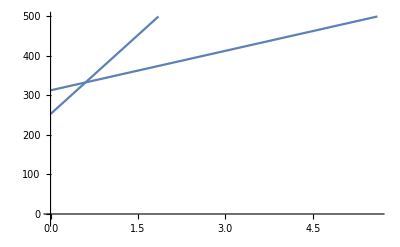

```mathematica
Plot[{g1,g2,g3}+273, {t, 0,13}, PlotRange->{All, {-20,500}}]
```

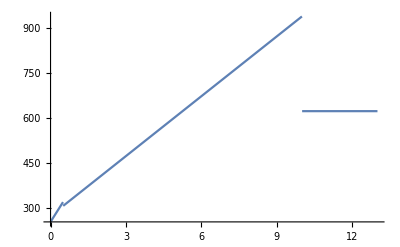

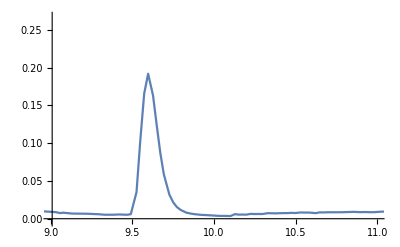

```mathematica
ListLinePlot[Select[data2, #[[1]][[1]] ==2& ][[92]][[All,{2,11}]]
,ImageSize->Full
, PlotRange->{{9,11}, All}
]
```

```mathematica
points={{9.550842017507295,0.10331827714592168},{9.660337640683618,0.10331827714592168}}
```

{{9.55084,0.103318},{9.66034,0.103318}}

```mathematica
points[[2,1]]-points[[1,1]]
```

0.109496

```mathematica
9.698-9.581
```

0.117

```mathematica
6.66-6.73
```

-0.07

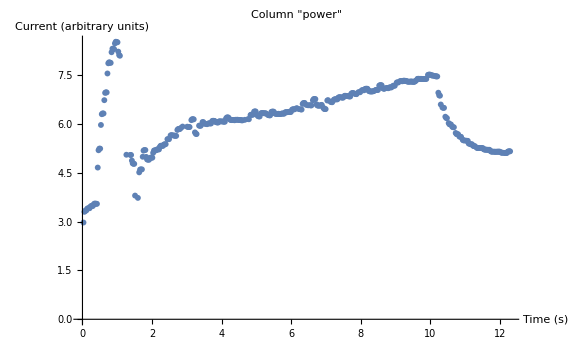

```mathematica
ListPlot[Select[data2, #[[1]][[1]] ==2& ][[91]][[All,{2,5}]]
, AxesLabel->{"Time (s)"," Current (arbitrary units)"}
, PlotLabel->"Column \"power\""
, ImageSize->Large
]
```

Delete wrong data:

First identify index of wrong data

```mathematica
Select[data2, #[[1]][[1]] ==2& ][[107]][[All,2]]
```

{0.033,0.056,0.079,0.114,0.137,0.159,0.182,0.207,0.23,0.252,0.274,0.297,0.319,0.341,0.365,0.387,0.409,0.448,0.471,0.494,0.516,0.538,0.561,0.583,0.622,0.645,0.667,0.69,0.714,0.737,0.759,0.782,0.821,0.845,0.867,0.889,0.923,0.946,0.968,0.991,1.032,1.054,1.078,1.118,1.141,1.163,1.186,1.215,1.238,1.261,1.283,1.317,1.34,1.363,1.385,1.407,1.441,1.463,1.485,1.525,1.548,1.571,1.593,1.616,1.638,1.661,1.683,1.705,1.745,1.767,1.789,1.819,1.842,1.864,1.888,1.91,1.932,1.955,1.977,1.999,2.025,2.047,2.069,2.091,2.113,2.136,2.158,2.18,2.202,2.242,2.265,2.287,2.309,2.332,2.355,2.377,2.399,2.422,2.444,2.466,2.488,2.511,2.534,2.557,2.579,2.619,2.641,2.664,2.686,2.718,2.74,2.763,2.785,2.809,2.831,2.854,2.875,2.898,2.92,2.942,2.964,2.987,3.009,3.032,3.055,3.078,3.119,3.142,3.165,3.187,3.215,3.24,3.263,3.285,3.323,3.349,3.371,3.393,3.432,3.455,3.478,3.5,3.534,3.556,3.578,3.618,3.64,3.663,3.686,3.711,3.734,3.757,3.779,3.817,3.84,3.863,3.885,3.913,3.936,3.958,3.981,4.017,4.04,4.063,4.085,4.117,4.14,4.162,4.184,4.21,4.234,4.257,4.279,4.301,4.341,4.364,4.386,4.411,4.439,4.461,4.483,4.515,4.538,4.56,4.583,4.613,4.636,4.658,4.68,4.712,4.734,4.757,4.779,4.813,4.836,4.86,4.882,4.911,4.933,4.955,4.978,5.,5.035,5.058,5.08,5.106,5.128,5.152,5.174,5.197,5.219,5.241,5.264,5.286,5.311,5.335,5.359,5.381,5.403,5.44,5.464,5.486,5.514,5.537,5.561,5.583,5.609,5.632,5.655,5.677,5.699,5.722,5.746,5.768,5.79,5.82,5.845,5.868,5.89,5.914,5.937,5.961,5.983,6.01,6.032,6.054,6.077,6.099,6.122,6.145,6.167,6.189,6.211,6.233,6.256,6.278,6.313,6.337,6.36,6.382,6.419,6.441,6.465,6.487,6.51,6.533,6.556,6.578,6.611,6.633,6.655,6.677,6.7,6.722,6.744,6.767,6.79,6.814,6.838,6.86,6.883,6.907,6.93,6.954,6.977,6.999,7.021,7.045,7.07,7.093,7.115,7.139,7.162,7.184,7.209,7.231,7.253,7.276,7.298,7.32,7.343,7.366,7.388,7.411,7.433,7.457,7.479,7.513,7.536,7.56,7.582,7.608,7.632,7.655,7.677,7.699,7.721,7.745,7.767,7.789,7.813,7.836,7.859,7.882,7.908,7.931,7.954,7.977,7.999,8.022,8.044,8.066,8.088,8.111,8.133,8.155,8.177,8.2,8.234,8.257,8.279,8.306,8.33,8.352,8.375,8.397,8.419,8.442,8.464,8.487,8.511,8.534,8.557,8.579,8.605,8.628,8.651,8.673,8.696,8.718,8.741,8.765,8.787,8.81,8.833,8.855,8.877,8.913,8.935,8.959,8.981,9.007,9.03,9.052,9.077,9.099,9.122,9.144,9.166,9.191,9.221,9.244,9.266,9.289,9.311,9.333,9.358,9.38,9.411,9.434,9.457,9.479,9.509,9.531,9.555,9.577,9.599,9.622,9.646,9.668,9.69,9.713,9.736,9.759,9.781,9.814,9.837,9.859,9.882,9.908,9.93,9.954,9.976,9.998,10.021,10.043,10.066,10.088,10.114,10.137,10.16,10.183,10.21,10.233,10.256,10.278,10.313,10.337,10.359,10.381,10.409,10.432,10.453,10.476,10.498,10.52,10.543,10.565,10.587,10.61,10.632,10.656,10.678,10.7,10.736,10.76,10.782,10.814,10.836,10.858,10.881,10.908,10.93,10.955,10.977,10.999,11.022,11.044,11.066,11.089,11.111,11.133,11.155,11.178,11.2,11.222,11.244,11.267,11.289,11.312,11.334,11.358,11.381,11.413,11.436,11.46,11.482,11.512,11.535,11.558,11.581,11.606,11.629,11.652,11.675,11.697,11.727,11.75,11.774,11.824,11.846,11.869,11.891,11.925,11.948,11.971,11.993,12.016,12.038,12.062,12.086,12.116,12.139,12.161,12.183,12.217,12.241,12.264,12.286,12.309,12.332,12.354,12.377,12.4,12.422,12.446,12.468,12.491,12.513,12.536,12.558,12.58,12.617,12.64,12.664,12.686,12.709,12.731,12.755,12.777,12.799,12.822,12.845,12.867,12.89,12.921,12.944,12.966,12.989}

Delete wrong data:

```mathematica
data2[[107*3+1+2]]=0
```

0

Check that data was deleted

```mathematica
data2[[109*3+1+2]][[-12;;-1]]
```

{{2,12.543,304.292,339.084,5.62898,6.11005,2.03211×10^7,-818256.,623.975,631.091,0.051535,629.374,-0.0122833,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.565,304.293,339.085,5.62948,6.1097,2.03214×10^7,-818565.,624.021,631.109,0.0514587,629.225,-0.012323,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.588,304.294,339.097,5.62956,6.11065,2.03207×10^7,-817978.,624.073,631.129,0.0513306,629.371,-0.0124054,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.61,304.293,339.077,5.63014,6.10977,2.03209×10^7,-817792.,624.078,631.125,0.0511719,629.117,-0.0124908,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.636,304.292,339.096,5.5837,6.05612,2.03232×10^7,-815319.,624.035,631.075,0.051297,628.567,-0.0121246,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.658,304.291,339.077,5.55763,6.03091,2.03235×10^7,-816463.,624.128,631.165,0.0512878,629.088,-0.0122833,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.681,304.291,339.077,5.55432,6.02879,2.03216×10^7,-816958.,624.1,631.165,0.0511505,629.339,-0.0126221,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.713,304.295,339.077,5.55583,6.0275,2.03211×10^7,-815350.,624.128,631.153,0.0510529,628.84,-0.012735,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.735,304.293,339.101,5.53895,6.01089,2.0324×10^7,-815195.,624.152,631.109,0.0510132,629.129,-0.0126862,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.758,304.293,339.094,5.53032,6.00199,2.03235×10^7,-815597.,624.228,631.211,0.0510376,629.21,-0.0126617,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.78,304.293,339.102,5.52975,6.00178,2.03237×10^7,-815319.,624.24,631.227,0.0511139,629.28,-0.0128387,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.81,304.292,339.11,5.53023,6.00126,2.03217×10^7,-815350.,624.219,631.232,0.0510315,629.102,-0.0127441,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15}}

```mathematica
Drop[data2, {42*3+1+2,
```

Examine data in relation with temperature:

```mathematica
Manipulate[
ListPlot[
Select[data2, #[[1]][[1]] ==2& ][[gcrun]][[All,{2,dataset}]]
, PlotLabel ->values[[dataset]]
,PlotRange->{{0,12},{0,10}}
,AxesLabel->{"Time (s)"}
, Epilog->{Scale[
Point[
Select[data2, #[[1]][[1]] ==2& ][[gcrun]][[All,{2,12}]]
]
,{1,1/70.0}
,{0,0}
]
}
](* Ends ListLine Plot*)
,{{gcrun,1,"GC Run"},1, Length[d1],1}
,{{dataset,11, "Dataset"},1,18,1}
] (* Ends Manipulate *)
```

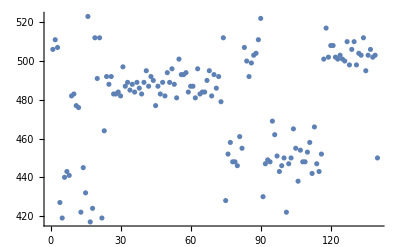

```mathematica
Length/@ data2d[[Range[Length[data2d]]]]//ListPlot
```

Print an SFC time to see if it looks sane

```mathematica
d1[[1]]
```

659.9

Create 3D values {t_r1,t_r2,det}

```mathematica
Clear[f]
```

```mathematica
f[x_, y_]:= {Map[Prepend[#,x]&,y]}
```

The number of GC runs:

```mathematica
Select[data2, #[[1]][[1]] ==2& ][[All, All,{2,11}]]//Length
```

140

```mathematica
Length[d1]
```

140

```mathematica
data2d =Inner[f, d1, Select[data2, #[[1]][[1]] ==2& ][[All, All,{2,11}]], Join];
```

```mathematica
params //TableForm
```

GC column description:	Rxi-5Sil MS 0.250 mm x 1 m
SFC flow rate:	0.800
SFC temperature:	22.000
GC flow rate: 	99.000
Experiment title: 	Diesel PAH
Sample name: 	10% Aromatics in diesel Total (TM) 50 ppm
Analysis type: 	Standard
Concentration: 	9999.000
Operator name: 	DM
Detector sensitivity: 	1.0E-8
FID H2 flow rate: 	36.700
FID Air flow rate: 	300.000
SFC pressure: 	20265000 Pa
SFC dead time: 	660.000 s
File name: 	C:\SFC-GC\Data\2020_02_11-120014.dat
SFC gradient0:
Rate: 	0 $1 s^-1
Final:	0.000000 $1
Time:	960.000 s
GC gradient0:
Rate: 	0 $1 s^-1
Final:	253.150000 $1
Time:	0.000 s
GC gradient1:
Rate: 	133 $1 s^-1
Final:	333.150000 $1
Time:	0.000 s
GC gradient2:
Rate: 	33 $1 s^-1
Final:	623.150000 $1
Time:	2.000 s
GC idle temperature:	303.100000 Cdeg
GC purge temperature: 	473.150000 Cdeg
GC sampling temperature: 	258.150000 Cdeg
GC sampling time: 	3
GC load time: 	3
GC vent time: 	1

```mathematica
plot3d = ListPlot3D[
Flatten[data2d,1]
,PlotRange->{All, All, All}
,AxesLabel->{"SFC (s)", "GC (s)","Detector (V)"}
,PlotLabel->StringSplit[params[[6]], ":"][[2]]
,Mesh -> None
,ImageSize->Large
(*, ColorFunction->"BlueGreenYellow"*)
]
```

-Graphics3D-

```mathematica
EmitSound[Sound[SoundNote[]]]
```

```mathematica
fudge =Table[0,Length[data2d]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Rt[90] = 5,67905
Rt[91] = 5,80543
Rt[92] = 5,69485

This is what we want Rt[91] to be:

```mathematica
Mean[{5.67905,5.69485}]
```

5.68695

Fudge for Rt[91]:

```mathematica
fudge[[91]]=5.80543 -Mean[{5.67905,5.69485}]
```

0.11848

```mathematica
fudge
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.11848,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
fdata2d =data2d;
```

```mathematica
fdata2d[[91,All,2]]+=fudge[[91]]
```

{0.14748,0.17348,0.19648,0.22648,0.25048,0.27348,0.29748,0.32448,0.34848,0.37148,0.39448,0.41748,0.44048,0.46348,0.48748,0.51248,0.53448,0.55748,0.58048,0.60348,0.62748,0.64948,0.67348,0.69748,0.72448,0.74648,0.76948,0.79148,0.81448,0.83648,0.86048,0.88248,0.90648,0.92948,0.95448,0.97948,1.00248,1.02748,1.05148,1.07548,1.09748,1.12548,1.14748,1.17248,1.19448,1.38148,1.49248,1.51648,1.53948,1.56248,1.58448,1.60648,1.63048,1.71148,1.74948,1.77448,1.79648,1.82748,1.85048,1.87348,1.89648,1.92648,1.95048,1.97448,1.99648,2.03048,2.05348,2.07848,2.10248,2.12748,2.15048,2.17448,2.19748,2.22748,2.24948,2.27248,2.29448,2.31748,2.34148,2.36448,2.38748,2.41048,2.43248,2.45548,2.47748,2.51048,2.56048,2.58348,2.60648,2.65148,2.67548,2.69848,2.74248,2.76548,2.78948,2.81248,2.84648,2.86948,2.89248,2.91648,2.94948,2.99648,3.12748,3.15148,3.17448,3.19748,3.24848,3.27048,3.29348,3.31648,3.35148,3.37548,3.39848,3.47048,3.49348,3.51648,3.57048,3.59348,3.61848,3.67648,3.70048,3.74548,3.76848,3.79048,3.81448,3.84748,3.86948,3.89348,3.91648,3.94948,3.97248,3.99548,4.01748,4.04548,4.06948,4.10548,4.14348,4.16648,4.18948,4.21148,4.24548,4.26848,4.29048,4.31348,4.34748,4.37148,4.39348,4.41548,4.44848,4.47148,4.49448,4.51848,4.56448,4.59348,4.61748,4.64848,4.67148,4.69448,4.71748,4.78648,4.87948,4.90248,4.94948,4.97148,4.99448,5.01748,5.05248,5.07548,5.09848,5.14448,5.16648,5.18848,5.21248,5.24948,5.27248,5.29548,5.31748,5.34948,5.37448,5.39648,5.44448,5.46748,5.49048,5.51248,5.54748,5.56948,5.59348,5.61648,5.64348,5.66648,5.69048,5.71248,5.74748,5.77048,5.79348,5.81548,5.84648,5.87048,5.89348,5.91548,5.95148,5.97348,5.99648,6.03848,6.06248,6.08548,6.10848,6.14148,6.16548,6.18848,6.21148,6.26948,6.29248,6.34748,6.39348,6.41748,6.44748,6.47148,6.50448,6.55548,6.60648,6.65248,6.67648,6.69948,6.74248,6.76648,6.79048,6.81348,6.84548,6.86848,6.89148,6.91348,6.94848,6.97048,6.99748,7.03948,7.06348,7.08548,7.10848,7.15648,7.17848,7.25148,7.27448,7.29748,7.34248,7.36648,7.38848,7.41148,7.44448,7.46748,7.49348,7.51648,7.54348,7.56848,7.59048,7.61348,7.65248,7.67548,7.69748,7.74448,7.76748,7.79148,7.81548,7.84148,7.86548,7.88848,7.91148,7.95148,7.97448,7.99648,8.04948,8.07548,8.09948,8.14448,8.16748,8.19048,8.21448,8.24448,8.26748,8.29048,8.31248,8.34448,8.36748,8.39148,8.41448,8.44748,8.47048,8.49648,8.54448,8.56648,8.58848,8.61248,8.64848,8.67248,8.69448,8.71748,8.74748,8.77248,8.79548,8.84348,8.86648,8.89048,8.91248,8.95048,8.97648,9.00048,9.04848,9.07348,9.09648,9.15248,9.17648,9.19948,9.24848,9.27248,9.29548,9.31748,9.34848,9.37148,9.39548,9.41748,9.44548,9.46748,9.49248,9.51348,9.54548,9.56848,9.59148,9.61348,9.63648,9.65848,9.68248,9.70548,9.74648,9.76948,9.79348,9.81648,9.84848,9.87348,9.89648,9.92048,9.95448,9.97748,10.0025,10.0505,10.0725,10.0955,10.1175,10.1515,10.1745,10.1995,10.2485,10.2705,10.2935,10.3175,10.3485,10.3725,10.3955,10.4185,10.4655,10.4885,10.5115,10.5495,10.5735,10.5955,10.6455,10.6675,10.6895,10.7115,10.7495,10.7725,10.7955,10.8475,10.8705,10.8935,10.9165,10.9525,10.9785,11.0015,11.0495,11.0725,11.1005,11.1505,11.1735,11.1955,11.2215,11.2695,11.2935,11.3165,11.3505,11.3745,11.3995,11.4485,11.4725,11.4945,11.5175,11.5545,11.5785,11.6015,11.6255,11.6495,11.6725,11.6955,11.7175,11.7485,11.7715,11.7955,11.8185,11.8465,11.8685,11.8905,11.9145,11.9525,11.9745,11.9965,12.0235,12.0475,12.0695,12.0925,12.1145,12.1535,12.1765,12.1985,12.2455,12.2695,12.2915,12.3155,12.3415,12.3665,12.3895,12.4115}

```mathematica
plot3d = ListPlot3D[
Flatten[fdata2d,1]
,PlotRange->{All, All, All}
,AxesLabel->{"SFC (s)", "GC (s)","Detector (V)"}
,PlotLabel->StringSplit[params[[6]], ":"][[2]]
,Mesh -> None
,ImageSize->Large
(*, ColorFunction->"BlueGreenYellow"*)
]
```

-Graphics3D-

```mathematica
Show[plot3d, PlotRange->{{680,960},{7,15},{0,5}}]
```

-Graphics3D-

```mathematica
Show[plot3d, PlotRange->{{400,1000},All,All}]
```

```mathematica
Slider[Dynamic[opac]]
```

```mathematica
color = Dynamic[RGBColor[1,0,0,1]]
```

```mathematica
Dynamic[a]
```

```mathematica
a=92
```

92

```mathematica
90
```

```mathematica
Dynamic[Graphics3D[{Black,Line[data2d[[a]]]}]]
```

```mathematica
Show[plot3d, Graphics3D[{color,Line[data2d]},Graphics3D[{Black,Line[data2d[[a]]]}]], PlotRange->All]
```

-Graphics3D-

Make a virtual SFC Chromatogram:

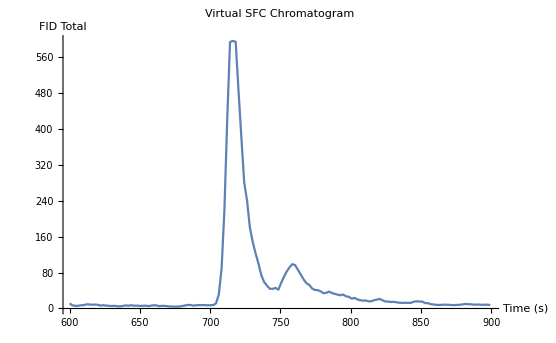

```mathematica
ListLinePlot[Partition[Riffle[d1,(Total[#]&/@data2d)[[All,3]]],2], PlotLabel->"Virtual SFC Chromatogram", AxesLabel->{"Time (s)","FID Total"}, PlotRange->{All, All}]
```

Create graphics for export to the thesis or publication:

```mathematica
exportgraphic = Show[
	plot3d
	,PlotLabel -> Style["FAMEs: Canola oil", Large, Bold, Black]
	, AxesStyle -> {Directive[Black, Bold, 15]
				, Directive[Black, Bold, 15]
				, Directive[Black, Bold, 15]
				}
	,AxesLabel-> 
		{Style["SFC (s)", Large, Bold, Black]
		, Style[ "GC (s)",Large, Bold, Black]
		,Style[Rotate["Detector (V)", 90 Degree], Large, Bold, Black]
		}
	(*, ViewPoint->{10000,10000,10000} *)
	, ImageSize-> 1024
	, ViewPoint->vp
	
]
```

```mathematica
Export["C:\\Users\\fskdm\\My PhD\\Conferences\\Analitika 2018\\Poster\\images\\Canola.png",exportgraphic,Background->None, ViewPoint->vp]
```

C:\Users\fskdm\My PhD\Conferences\Analitika 2018\Poster\images\Canola.png

```mathematica
Show[
	plot3d
(*	,Graphics3D[{Red,Line[data2d]}] *)
     , PlotLabel -> "Mystery Oil"
	, PlotRange-> {All, All,{0,0.1}}
]
```

```mathematica
contourplot = ListContourPlot[Flatten[data2d,1], PlotRange->{All, All, {0,5}}, AxesLabel->{"SFC (s)", "GC (s)"}]
```

-Graphics-

```mathematica
Show[contourplot, PlotRange->{All, All}]
```

-Graphics-